导入和导出

到目前为止，我们在本书中所做的一切都完全是在 Wolfram 语言和 Wolfram 知识库中完成的。但有时你需要从外部获取对象。不用说，它们往往不会像我们在 Wolfram 语言内部所习惯的那样干净和有组织，而且它们可能会在没有警告的情况下发生更改。

作为第一个例子，让我们从联合国网站的首页导入文本。我们可以使用函数 Import 来完成这个任务。

导入联合国网站首页的文本版本(现在可能有所不同)：

```mathematica
Import["http://un.org"]
```

الأمم المتحدة — إنها عالمك  
联合国，您的世界！  
United Nations — It's your world!  
Nations Unies — C'est votre monde!  
Организация Объединенных Наций — это ваш мир!  
Las Naciones Unidas son su mundo

结果是一个字符串，可能还有一些空白行。让我们先在换行处分割这个字符串。

在新行处分割，以得到一个字符串的列表：

```mathematica
StringSplit[Import["http://un.org"],"\n"]
```

{الأمم المتحدة — إنها عالمك, 联合国，您的世界！,United Nations — It's your world!,Nations Unies — C'est votre monde!,Организация Объединенных Наций — это ваш мир!,Las Naciones Unidas son su mundo}

确定每个字符串的语言(空白行被认为是英语)：

```mathematica
LanguageIdentify[StringSplit[Import["http://un.org"],"\n"]]
```

{Arabic,Chinese,English,French,Russian,Spanish}

Import 可以让你导入各种各样的不同元素。"Hyperlinks" 可以获取出现在网页上的超链接；"Images" 则会获取图像。

获取联合国网站首页的超链接列表：

```mathematica
Import["http://un.org","Hyperlinks"]
```

{//www.un.org/ar/index.html,//www.un.org/zh/index.html,//www.un.org/en/index.html,//www.un.org/fr/index.html,//www.un.org/ru/index.html,//www.un.org/es/index.html}

获取出现在维基百科首页的图片：

```mathematica
Import["http://wikipedia.org","Images"]
```

{-Graphics-,-Graphics-}

举一个更复杂的例子，这里有一个我的网站的部分超链接的图。为了便于管理，我只取了每一层的前 5 个超链接，而且只取了 3 层。

计算网站的部分超链接图：

```mathematica
NestGraph[Take[Import[#,"Hyperlinks"],5]&,"http://stephenwolfram.com",3]
```

-Graphics-

Wolfram 语言可以导入数百种格式，包括电子表格、图像、声音、几何图形、数据库、日志文件等等。Import 会自动查看文件扩展名(.png、.xls 等)，以确定要做什么。

从我的网站中导入图像：

```mathematica
Import["http://www.stephenwolfram.com/img/homepage/stephen-wolfram-portrait.png"]
```

-Graphics-

Wolfram 语言认出了我：

```mathematica
Classify["NotablePerson",%]
```

Stephen Wolfram

除了从网络上导入外，Import 也可以从您自己的文件中导入，这些文件存储在您的计算机系统或 Wolfram Cloud 中。

Wolfram 语言不仅可以让你处理网页和文件，还可以处理服务或 API。例如，SocialMediaData 可以让你从社交媒体服务中获取数据，至少在你授权他们发送数据之后。

找到我的 Facebook 朋友网络(需要授权访问他们的连接数据)：

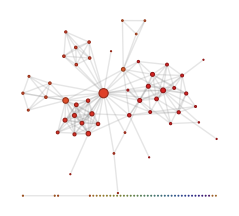

```mathematica
SocialMediaData["Facebook","FriendNetwork"]
```

Wolfram 语言可以访问的另一个外部服务是网络搜索。

用关键词“colorful birds”在网络上搜索图片：

```mathematica
WebImageSearch["colorful birds"]
```

Dataset[<>]

请求图像缩略图：

```mathematica
WebImageSearch["colorful birds","Thumbnails"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

他们被认为是不同种类的鸟：

```mathematica
ImageIdentify/@%
```

{indigo bunting,blue peafowl,mandarin duck,european goldfinch,rainbow lorikeet,ring-necked parakeet,bluebird,rainbow lorikeet,scrub-bird,rainbow lorikeet}

Wolfram 语言的一个重要的外部数据来源是 Wolfram 数据存储库。该数据库中的数据来自许多地方，但都被设置为易于在 Wolfram 语言中使用。

你可以通过浏览 Wolfram 数据存储库来了解有哪些可用的数据。

-Graphics-

一旦你找到了你想要的东西，只需使用 ResourceData["name"] 就可以把它输入到 Wolfram 语言中。

获取达尔文的《物种起源》全文，然后将它做成一个词云：

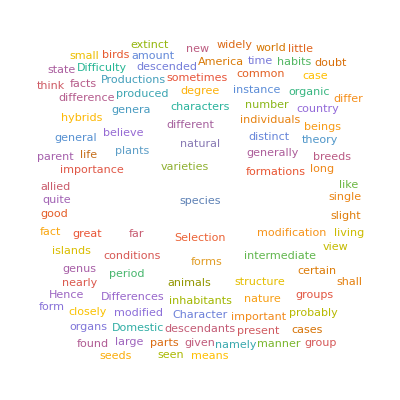

```mathematica
WordCloud[ResourceData["On the Origin of Species"]]
```

除了把东西输入到 Wolfram 语言中，你还可以把东西发送出去。例如，SendMail 可以从 Wolfram 语言中发送电子邮件。

通过电子邮件给自己发信息(对我来说是给我发)：

```mathematica
SendMail["Hello from the Wolfram Language!"]
```

-Graphics-

向一个测试账户发送电子邮件，主题为“狼”，并附上一张狼的图片：

```mathematica
SendMail["test@wolfram.com",{"Wolf","Here's a wolf...", -Graphics-}]
```

如果你想与外部程序和服务进行互动，你往往需要从 Wolfram 语言中导出一些东西。

将一个圆的图形以 PDF 格式导出到云端：

```mathematica
CloudExport[Graphics[Circle[ ]],"PDF"]
```

CloudObject[]

你也可以使用 Export 来将其导出到本地文件。

将素数及其幂的表导出到本地电子表格文件中：

```mathematica
Export["primepowers.xls",Table[Prime[m]^n,{m,10},{n,4}]]
```

primepowers.xls

下面是生成的文件的一部分：

-Graphics-

将文件的内容导回到 Wolfram语言中：

```mathematica
Import["primepowers.xls"]
```

{{{2.,4.,8.,16.},{3.,9.,27.,81.},{5.,25.,125.,625.},{7.,49.,343.,2401.},{11.,121.,1331.,14641.},{13.,169.,2197.,28561.},{17.,289.,4913.,83521.},{19.,361.,6859.,130321.},{23.,529.,12167.,279841.},{29.,841.,24389.,707281.}}}

Wolfram 语言可以导入和导出数百种不同类型的格式。

导出适合用于 3D 打印的 3D 几何图形：

```mathematica
Export["spikey.stl",LinguisticAssistant["Image"]]
```

spikey.stl

这是根据 spikey.stl 文件进行 3D 打印的结果：

-Graphics-

以适合打印的形式创建 3D 几何体可能是相当复杂的。函数 Printout3D 将自动完成所有的步骤，它还可以将最终的几何体发送给 3D 打印服务商(或者你自己的 3D 打印机，如果你有的话)。

创建一个随机的球体团块：

```mathematica
Graphics3D[Sphere[RandomReal[5,{30,3}]]]
```

-Graphics3D-

把这个发送到 Sculpteo 服务进行 3D 打印：

```mathematica
Printout3D[%,"Sculpteo"]
```

Dataset[<>]

-Graphics- |     | -Graphics-

词汇

Import[loc] |   | 从外部位置导入
SocialMediaData[...] |   | 从社交媒体网络获取数据
WebImageSearch["keyword"] |   | 在网络上进行图像搜索
ResourceData["name"] |   | 从 Wolfram 数据存储库中获取数据
SendMail[expr] |   | 发送邮件
CloudExport[expr,format] |   | 以某种格式导出到云端
Export[file,expr] |   | 导出到文件
Printout3D[source,"service"] |   | 将 source 发送到 3D 打印服务商

"共有 9 道习题" | "开始练习 »"

从 http://google.com 中导入图像。»

| 期望输出示例： |  
  | {-Graphics-,-Graphics-} |

使用 http://google.com 中的图像的主色来创建一个圆盘的图像拼贴。»

| 期望输出示例： |  
  | -Graphics- |

将 http://bbc.co.uk 上的文本创建为词云。»

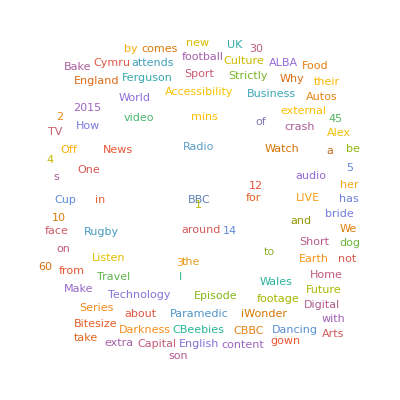
| 期望输出示例： |  
  | -Graphics- |

为  http://nps.gov 上的图片创建一个图像拼贴。»

| 期望输出示例： |  
  | -Graphics- |

使用 ImageInstanceQ 在 https://en.wikipedia.org/wiki/Ostrich 中找出鸟类的图片。»

| 期望输出示例： |  
  | {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-} |

使用 TextCases 在 http://nato.int 中找出所有国家名称的实例，并将其创建为一个词云。»

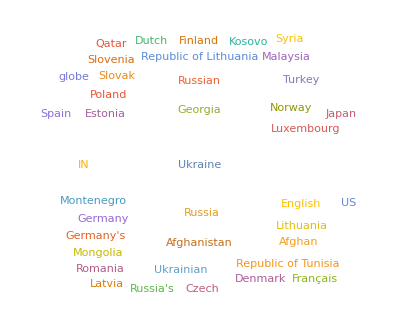
| 期望输出示例： |  
  | -Graphics- |

找出 https://en.wikipedia.org 中的链接数量。»

| 期望输出示例： |  
  | 292 |

给自己发送一个带有你当前位置地图的邮件。»

| 期望输出示例： |  
  | {"MessageID"→"27542834033679034197.0.WolframLanguage.7Qo3YdBo"} |

给自己发送包含当前月相的图标的邮件。»

| 期望输出示例： |  
  | {"MessageID"→"27542858880723918541.0.WolframLanguage.7Qo3YdBo"} |

问&答

为什么我在运行网站示例时得到不同的结果？

因为这些网站已经发生变化了！现在网站上有什么，你得到的就是什么。

为什么 Import 不能检索到我在浏览器中访问网页时看到的元素？

可能是因为它们没有直接出现在网页的 HTML 源代码中，而这正是 Import 查看的内容。它们可能是用 JavaScript 动态加载的。

如果我正在使用云端，我可以从我的电脑上导入一个本地文件吗？

可以。使用云端系统中的上传按钮 ，来将文件上传到你的云端文件系统中，然后使用 Import。

Import 可以处理哪些格式？

参见 wolfr.am/ref-importexport 中的列表或者计算 $ImportFormats。

Import 和 Export 如何确定要使用哪种格式？

你可以明确地指定。否则他们将使用文件扩展名来确定，比如 .gif 或者 .mbox。

Export 将其创建的文件放在哪里？

如果你在指定的文件名中没有给出一个目录，它就会放在你的当前目录。你可以使用 SystemOpen 来使用你的操作系统来打开它，你也可以用 DeleteFile 来删除它。

什么是 API？

应用程序接口(Application Program Interface)。它是一个程序向其他程序，而不是向人类公开的接口。Wolfram 语言有非常多 API，并允许你使用 APIFunction 来创建你自己的 API。

我如何授权连接到我的一个外部账户？

当你使用 SocialMediaData 或者 ServiceConnect 时，通常会提示您授权 Wolfram Connection 应用程序使用该特定服务。

技术笔记

ImportString 让你从一个字符串中“导入”，而不是从一个外部文件或 URL。ExportString 将“导出”到一个字符串。

SendMail 将使用您设置的首选邮件服务器，或者 Wolfram Cloud 中的代理。

Wolfram 语言支持多种外部服务。通常，它使用像 OAuth 这样的机制来验证它们。

另一种获取(和发送)数据的方式是将你的计算机直接连接到传感器、Arduino 等。Wolfram 语言有一个完整的框架来处理这类事情，包括 DeviceReadTimeSeries 等函数。

如果你是在你的本地计算机上运行所有的东西，你可以让 Wolfram 语言来启动外部程序，并与它们交换数据，例如，使用 RunProcess。在简单的情况下，你通常可以直接从一个程序中输入数据，比如使用 Import["!program",...]。

Wolfram 语言支持数据的异步读取和写入。一个简单的例子是 URLSubmit，但 ChannelListen 等允许你建立一个完整的中介发布-订阅系统。

探索更多

Wolfram 语言中的导入和导出指南 »